# SMRTNE ŽRTVE SKOZI DRUGO SVETOVNO VOJNO

## Pripravil: Alen Rajšel, ROM, 2022/23

## PRIDOBIVANJE PODATKOV:

Vse prikazane podatke sem dobil iz wikipedije:

https://en.wikipedia.org/wiki/Siege_of_Warsaw_(1939)
https://en.wikipedia.org/wiki/Battle_of_France
https://en.wikipedia.org/wiki/Battle_of_Moscow
https://en.wikipedia.org/wiki/Battle_of_Stalingrad#Casualties
https://en.wikipedia.org/wiki/Battle_of_Berlin
https://en.wikipedia.org/wiki/Second_Battle_of_the_Marne
https://en.wikipedia.org/wiki/Battle_of_Passchendaele
https://en.wikipedia.org/wiki/Gallipoli_campaign
https://en.wikipedia.org/wiki/Battle_of_Tannenberg
https://en.wikipedia.org/wiki/Battle_of_the_Somme

```mathematica
skupnezrtve2= Import["C:\\Users\\alen\\Desktop\\WW2.xlsx", "Data"]
skupnezrtve1= Import["C:\\Users\\alen\\Desktop\\ww1.xlsx", "Data"]
bitkanasomi = Import["C:\\Users\\alen\\Desktop\\bitka na somi.xlsx", "Data"]
bitkazastalingrad = Import["C:\\Users\\alen\\Desktop\\bitka za stalingrad.xlsx", "Data"]
```

## UVOD:

Druga svetovna vojna, trajajoča od 1939 do 1945, je združila večino držav v zaveznike in sile ose. Konflikt je izbruhnil z Hitlerjevim napadom na Poljsko leta 1939, kar je privedlo do vstopa zahodnih držav v vojno. Boji so potekali na številnih frontah, vključno z Evropo, Azijo, Afriko in Pacifikom. Osi, sestavljene iz Nemčije, Italije in Japonske, so se spopadale z zavezniki, kot so Združeno kraljestvo, ZDA in Sovjetska zveza. Vojna je prinesla tragične dogodke, kot so holokavst in uporaba jedrske bombe na Hirošimo ter Nagasaki, ter pustila za seboj mnoge bitke s številnimi žrtvami. Leta 1945 so zavezniške sile dosegle zmago s kapitulacijo Nemčije in Japonske, kar je imelo dolgoročne posledice za svetovno politiko in družbo.

## ŽRTVE V BITKAH SKOZI ČAS:

## GRAF SKUPNIH ŽRTEV V NAJBOLJ KRVAVIH BITKAH DRUGE SVETOVNE VOJNE:

Za vsako posamezno leto sem dobil podatke o skupnih smrtnih žrtvah pri najbolj krvavih bitkah druge svetovne vojne. 
Leta 1939 je Nemčija napadla Poljsko, najbolj krvava bitka je bila Bitka za Varšavo.
1940 je napadla Francijo in bitki se je imenovalo Bitka za Francijo. 
Leto pozneje se je zgodila Bitka za Moskvo.
1942 je bila najbolj krvava bitka druge svetovne vojne imenovana Bitka za Stalingrad.
1943 je bila največja tankovska bitka imenovana Bitka pri Kursku .
1944 se je zgodila Operacija Overlord, bolj znana po imenu Dan D.
1945 je bila zadnja bitka v Evropi in sicer Bitka za Berlin.

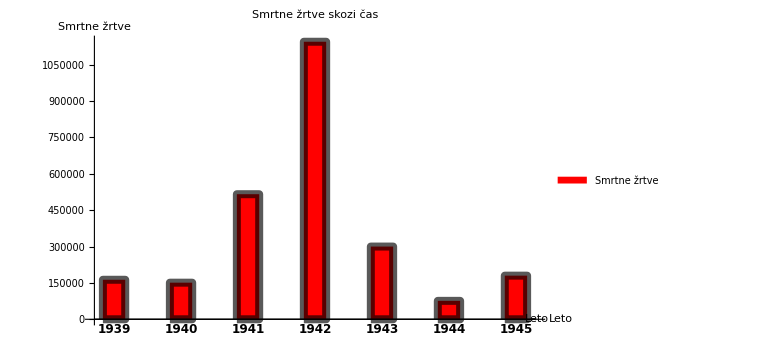

```mathematica
years=IntegerPart/@Rest[skupnezrtve2[[1,1]]];
fatalities=Rest[skupnezrtve2[[1,2]]];

BarChart[fatalities,ChartLabels->Placed[Style[#,12,Bold,Black]&/@years,Below],ChartStyle->Directive[Red,EdgeForm[{Black,Thickness[0.01]}]],BarSpacing->{2,1},ChartLegends->Placed[{"Smrtne žrtve"},Top],AxesLabel->{"Leto","Smrtne žrtve"},PlotLabel->"Smrtne žrtve skozi čas",ImageSize->Large]
```

## PRVA SVETOVNA VOJNA:

Prva svetovna vojna je imela veliko manj žrtev, najbolj krvave bitke so bile Bitka za Tanenberg, Bitka za Galipoli, Bitka na Somi, Bitka za Pachandale, Druga bitka na Marni.

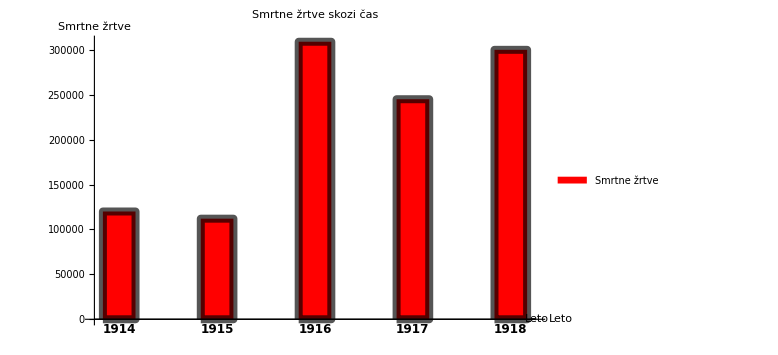

```mathematica
years=IntegerPart/@Rest[skupnezrtve1[[1,1]]];
fatalities=Rest[skupnezrtve1[[1,2]]];

BarChart[fatalities,ChartLabels->Placed[Style[#,12,Bold,Black]&/@years,Below],ChartStyle->Directive[Red,EdgeForm[{Black,Thickness[0.01]}]],BarSpacing->{2,1},ChartLegends->Placed[{"Smrtne žrtve"},Top],AxesLabel->{"Leto","Smrtne žrtve"},PlotLabel->"Smrtne žrtve skozi čas",ImageSize->Large]
```

## PRIMERJAVA DVEH NAJVEČJIH BITK

#### Bitka na Somi:

Bila je največja bitka prve svetovne vojne, trajala je od 1.7.1914 do 18.11.1914. Borili so se Nemci(Centralne sile) proti Angleži in Francozi(Antantne sile).

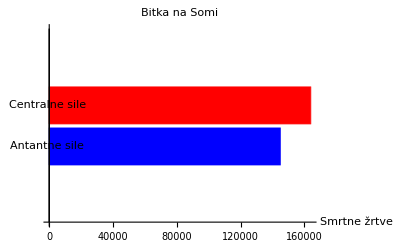

```mathematica
BarChart[MapThread[Style[#1,#2]&,{bitkanasomi[[1,All,2]],{Blue,Red}}],ChartLabels->bitkanasomi[[1,All,1]],AxesLabel->{"","Smrtne žrtve"},PlotLabel->"Bitka na Somi",BarOrigin->Left,ChartLayout->"Grouped"]
```

#### Bitka za Stalingrad:

Bila je največja bitka druge svetovne vojne, trajala je od 23.8. 1942 do 2.2. 1943. Borila se je Nemčija, Romunija, Italija, Madžarska, Hrvaška, oni so se imenovali Sile osi. 
Borili so se pa proti Sovjetski zvezi, ki je bila na strani zaveznikov.

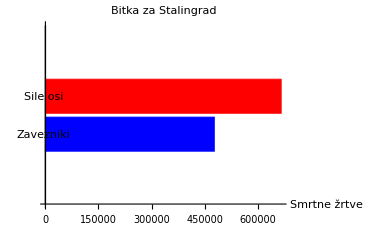

```mathematica
BarChart[MapThread[Style[#1,#2]&,{bitkazastalingrad[[1,All,2]],{Blue,Red}}],ChartLabels->bitkazastalingrad[[1,All,1]],AxesLabel->{"","Smrtne žrtve"},PlotLabel->"Bitka za Stalingrad",BarOrigin->Left,ChartLayout->"Grouped"]
```